```mathematica
SetDirectory["D:\\Chaozhi\\GitHub Clones\\TetraOrigin\\TetraOrigin_Packages"];
Needs["TetraOrigin`"]
SetDirectory[NotebookDirectory[]]
```

D:\Chaozhi\GitHub Clones\TetraOrigin\TetraOrigin_Tutorial

```mathematica
dataid="simSNPDose";
SNPDosefile="simSNPDose.csv";
{chrsubset,snpsubset}={"All","All"};
epsF=0;
eps=10^(-3.);
ploidy=4;
outputid=dataid;
```

```mathematica
SNPDose=Import[SNPDosefile];
Dimensions[SNPDose]
SNPDose[[;;10,;;10]]//MatrixForm
```

{55,76}

(marker | SNP1 | SNP2 | SNP3 | SNP4 | SNP5 | SNP6 | SNP7 | SNP8 | SNP9
chromosome | A | A | A | A | A | A | A | A | A
position_cM | 0.1578 | 1.6068 | 3.8056 | 5.1862 | 6.9518 | 7.9891 | 9.5328 | 11.9003 | 13.5111
parent1 | 1 | 2 | 2 | 0 | 2 | 1 | 3 | 3 | 3
parent2 | NA | 1 | 2 | 2 | 2 | NA | 3 | 1 | 2
sib1 | NA | 1 | 1 | 2 | 1 | 2 | NA | 2 | 3
sib2 | 2 | 2 | 1 | 1 | 3 | 1 | 3 | 2 | 3
sib3 | 2 | 2 | 0 | 1 | 2 | 2 | 3 | 3 | 2
sib4 | 3 | 2 | 1 | 1 | 2 | 3 | NA | 3 | 2
sib5 | 3 | 1 | 2 | 1 | 2 | 2 | 4 | 2 | 4)

```mathematica
(*****************************************************************************************************************************)
```

```mathematica
??inferTetraOrigin
```

inferTetraOrigin[SNPDose, chrsubset, snpsubset, eps, founderhaplo, ploidy, outputid] calculates the posterior probabilities for each sib at each SNP marker given the the parental haplotype founderhaplo, and the results are saved in the file "TetraOrigin_Output_outputid_LinkageGroupA.txt" for the linkage group A, and so on for the rest linkage groups. Refer to inferTetraPhase for estimating parental haplotype and descriptions of other paremters. 
inferTetraOrigin[SNPDose, chrsubset, snpsubset, eps, epsF, ploidy, outputid] is a combination of {founderhaplo, loglhistory}= inferTetraPhase[SNPDose, chrsubset, snpsubset, eps, epsF,ploidy] and inferTetraOrigin[SNPDose, chrsubset, snpsubset, eps, epsF,ploidy, founderhaplo, outputid].

Attributes[inferTetraOrigin]={Protected,ReadProtected}
 
Options[inferTetraOrigin]={maxStuck→10,maxIteration→100,minRepeatRun→3,maxPhasingRun→20,bivalentPhasing→True,bivalentDecoding→False}

```mathematica
inferTetraOrigin[SNPDosefile,chrsubset,snpsubset,eps,epsF,ploidy,outputid,bivalentPhasing->True,bivalentDecoding->False];
```

Start Date =Thu 19 May 2016 15:27:48. Chromosome  = A

Finish Phasing Date =Thu 19 May 2016 15:29:07. Time used in Phasing = 79.8 Seconds. log posterior of phasing runs = {-1744.65,-2029.22,-1744.65,-1744.65}

Start Date =Thu 19 May 2016 15:29:07. Outputfile=TetraOrigin_Output_simSNPDose_LinkageGroupA.txt

Finish Date =Thu 19 May 2016 15:29:29. Time used in Posteriordecoding = 21.3 Seconds.

--------------------------------------------------------------------------------------

```mathematica
(*****************************************************************************************************************************)
```

```mathematica
linkagegroup="A";
tetraResultFile="TetraOrigin_Output_"<>dataid<>"_LinkageGroup"<>ToString[linkagegroup]<>".txt"
summaryFile=StringReplace[tetraResultFile,{".txt"->"_Summary.csv"}]
```

TetraOrigin_Output_simSNPDose_LinkageGroupA.txt

TetraOrigin_Output_simSNPDose_LinkageGroupA_Summary.csv

```mathematica
FileExistsQ[tetraResultFile]
```

True

```mathematica
refhaploFile="trueParentPhase.csv"
saveAsSummaryITO[tetraResultFile,summaryFile];//AbsoluteTiming
```

trueParentPhase.csv

{5.55434,Null}

```mathematica
(*****************************************************************************************************************************)
```

```mathematica
?getSummaryITO
```

getSummaryITO[summaryFile] imports the summary produced by saveAsSummaryITO for furthur analysis in mathematica, and returns {description, snpmap, esthaplo, refhaplo, logllist, siblogl, genotypes, estgenoprob, esthaploprob}, where description is a list of explainations for the rest.

```mathematica
{description,snpmap,esthaplo,refhaplo,logllist,siblogl,genotypes,estgenoprob,esthaploprob}=getSummaryITO[summaryFile];//AbsoluteTiming
Dimensions[#]&/@{description,snpmap,esthaplo,refhaplo,logllist,siblogl,genotypes,estgenoprob,esthaploprob}
description//MatrixForm
esthaplo[[3;;,2;;]]==refhaplo[[3;;,2;;]]
```

{0.62629,Null}

{{8,2},{76,3},{10,76},{1,1},{52,17},{51,7},{101,2},{50,75,100},{50,75,8}}

(inferTetraOrigin-Summary | Genetic map of biallelic markers
inferTetraOrigin-Summary | MAP of parental haplotypes
inferTetraOrigin-Summary | Reference haplotypes
inferTetraOrigin-Summary | ln marginal likelihood of each valent of each sib
inferTetraOrigin-Summary | ln marginal likelihood given the LG type of each sib
inferTetraOrigin-Summary | Genotypes in order
inferTetraOrigin-Summary | Conditonal genotype probability
inferTetraOrigin-Summary | Conditonal haplotype probability)

Part::take: Cannot take positions 3 through -1 in {{None}}.

```mathematica
{{1,2,1,1,2,1,1,2,1,1,1,1,1,2,2,1,1,2,1,1,2,1,1,1,2,1,1,2,2,2,1,1,1,2,1,1,2,1,2,1,2,2,2,1,1,2,1,1,1,2,1,2,2,1,1,2,2,1,2,2,2,2,2,2,1,1,1,2,1,2,1,2,2,2,1},{1,1,1,1,1,1,2,2,2,2,2,2,1,2,2,1,2,2,2,1,1,2,1,1,2,2,2,2,1,1,1,1,2,1,2,2,1,2,1,1,2,1,2,2,2,1,1,2,1,2,1,1,2,1,1,1,1,2,2,1,1,2,1,1,2,1,1,1,1,2,1,1,2,1,2},{2,1,2,1,1,2,2,2,2,1,2,2,1,1,2,1,1,1,2,1,1,2,2,2,1,1,2,1,1,1,1,1,1,2,2,1,1,1,1,2,1,1,1,1,1,1,1,2,2,1,2,1,1,2,1,1,1,2,1,1,1,2,2,2,1,1,1,2,1,1,2,2,1,2,1},{1,2,2,1,2,1,2,1,2,1,2,2,1,1,1,1,1,2,2,1,2,2,2,1,2,2,1,2,2,2,1,1,2,2,1,1,2,2,2,2,1,2,1,2,2,2,2,1,1,1,1,2,1,1,1,2,1,1,2,2,1,1,2,2,1,2,1,2,1,1,2,1,2,2,1},{1,1,2,1,1,1,1,1,1,1,2,2,1,1,1,1,2,2,1,2,2,1,1,1,1,1,1,2,1,1,1,1,1,2,2,2,1,1,2,1,1,2,1,2,2,1,2,2,2,1,2,1,1,2,2,2,1,2,2,1,2,1,2,1,2,2,2,1,1,2,1,2,1,2,2},{2,1,1,2,1,2,2,2,1,2,1,1,1,2,2,1,1,1,1,2,1,2,2,2,2,1,2,2,2,2,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,2,1,2,2,1,1,1,1,2,1,2,2,2,1,1,1,1,2,1,2,2,1,2,2,2,1,2,2,2,2},{2,2,1,1,2,2,2,1,2,2,2,1,1,2,2,2,1,1,1,1,1,1,2,1,2,1,2,1,2,1,2,2,1,1,1,1,2,1,2,1,1,1,1,2,2,1,2,1,1,2,1,2,2,1,1,2,2,2,1,1,2,1,1,2,1,1,1,2,1,1,1,2,1,2,2},{2,1,2,2,2,1,2,1,2,2,2,1,2,1,1,1,1,1,1,1,1,1,2,1,2,1,2,1,2,1,2,2,1,2,2,1,1,1,2,1,1,2,1,2,1,2,2,1,1,1,2,1,1,1,2,1,2,1,2,esthaplo//MatrixForm2,2,1,1,1,2,2,2,2,1,1,1,2,2,2,1}}=={{"None"}}⟦3;;All,2;;All⟧
```

```mathematica
esthaplo//MatrixForm
```

(SNP | SNP1 | SNP2 | SNP3 | SNP4 | SNP5 | SNP6 | SNP7 | SNP8 | SNP9 | SNP10 | SNP11 | SNP12 | SNP13 | SNP14 | SNP15 | SNP16 | SNP17 | SNP18 | SNP19 | SNP20 | SNP21 | SNP22 | SNP23 | SNP24 | SNP25 | SNP26 | SNP27 | SNP28 | SNP29 | SNP30 | SNP31 | SNP32 | SNP33 | SNP34 | SNP35 | SNP36 | SNP37 | SNP38 | SNP39 | SNP40 | SNP41 | SNP42 | SNP43 | SNP44 | SNP45 | SNP46 | SNP47 | SNP48 | SNP49 | SNP50 | SNP51 | SNP52 | SNP53 | SNP54 | SNP55 | SNP56 | SNP57 | SNP58 | SNP59 | SNP60 | SNP61 | SNP62 | SNP63 | SNP64 | SNP65 | SNP66 | SNP67 | SNP68 | SNP69 | SNP70 | SNP71 | SNP72 | SNP73 | SNP74 | SNP75
Chromosome | A | A | A | A | A | A | A | A | A | A | A | A | A | A | A | A | A | A | A | A | A | A | A | A | A | A | A | A | A | A | A | A | A | A | A | A | A | A | A | A | A | A | A | A | A | A | A | A | A | A | A | A | A | A | A | A | A | A | A | A | A | A | A | A | A | A | A | A | A | A | A | A | A | A | A
parent1_1 | 1 | 2 | 1 | 1 | 2 | 1 | 1 | 2 | 1 | 1 | 1 | 1 | 1 | 2 | 2 | 1 | 1 | 2 | 1 | 1 | 2 | 1 | 1 | 1 | 2 | 1 | 1 | 2 | 2 | 2 | 1 | 1 | 1 | 2 | 1 | 1 | 2 | 1 | 2 | 1 | 2 | 2 | 2 | 1 | 1 | 2 | 1 | 1 | 1 | 2 | 1 | 2 | 2 | 1 | 1 | 2 | 2 | 1 | 2 | 2 | 2 | 2 | 2 | 2 | 1 | 1 | 1 | 2 | 1 | 2 | 1 | 2 | 2 | 2 | 1
parent1_2 | 1 | 1 | 1 | 1 | 1 | 1 | 2 | 2 | 2 | 2 | 2 | 2 | 1 | 2 | 2 | 1 | 2 | 2 | 2 | 1 | 1 | 2 | 1 | 1 | 2 | 2 | 2 | 2 | 1 | 1 | 1 | 1 | 2 | 1 | 2 | 2 | 1 | 2 | 1 | 1 | 2 | 1 | 2 | 2 | 2 | 1 | 1 | 2 | 1 | 2 | 1 | 1 | 2 | 1 | 1 | 1 | 1 | 2 | 2 | 1 | 1 | 2 | 1 | 1 | 2 | 1 | 1 | 1 | 1 | 2 | 1 | 1 | 2 | 1 | 2
parent1_3 | 2 | 1 | 2 | 1 | 1 | 2 | 2 | 2 | 2 | 1 | 2 | 2 | 1 | 1 | 2 | 1 | 1 | 1 | 2 | 1 | 1 | 2 | 2 | 2 | 1 | 1 | 2 | 1 | 1 | 1 | 1 | 1 | 1 | 2 | 2 | 1 | 1 | 1 | 1 | 2 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 2 | 2 | 1 | 2 | 1 | 1 | 2 | 1 | 1 | 1 | 2 | 1 | 1 | 1 | 2 | 2 | 2 | 1 | 1 | 1 | 2 | 1 | 1 | 2 | 2 | 1 | 2 | 1
parent1_4 | 1 | 2 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 2 | 1 | 1 | 1 | 1 | 1 | 2 | 2 | 1 | 2 | 2 | 2 | 1 | 2 | 2 | 1 | 2 | 2 | 2 | 1 | 1 | 2 | 2 | 1 | 1 | 2 | 2 | 2 | 2 | 1 | 2 | 1 | 2 | 2 | 2 | 2 | 1 | 1 | 1 | 1 | 2 | 1 | 1 | 1 | 2 | 1 | 1 | 2 | 2 | 1 | 1 | 2 | 2 | 1 | 2 | 1 | 2 | 1 | 1 | 2 | 1 | 2 | 2 | 1
parent2_1 | 1 | 1 | 2 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 2 | 2 | 1 | 1 | 1 | 1 | 2 | 2 | 1 | 2 | 2 | 1 | 1 | 1 | 1 | 1 | 1 | 2 | 1 | 1 | 1 | 1 | 1 | 2 | 2 | 2 | 1 | 1 | 2 | 1 | 1 | 2 | 1 | 2 | 2 | 1 | 2 | 2 | 2 | 1 | 2 | 1 | 1 | 2 | 2 | 2 | 1 | 2 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 2 | 2 | 1 | 1 | 2 | 1 | 2 | 1 | 2 | 2
parent2_2 | 2 | 1 | 1 | 2 | 1 | 2 | 2 | 2 | 1 | 2 | 1 | 1 | 1 | 2 | 2 | 1 | 1 | 1 | 1 | 2 | 1 | 2 | 2 | 2 | 2 | 1 | 2 | 2 | 2 | 2 | 1 | 1 | 1 | 1 | 1 | 1 | 2 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 2 | 1 | 2 | 2 | 1 | 1 | 1 | 1 | 2 | 1 | 2 | 2 | 2 | 1 | 1 | 1 | 1 | 2 | 1 | 2 | 2 | 1 | 2 | 2 | 2 | 1 | 2 | 2 | 2 | 2
parent2_3 | 2 | 2 | 1 | 1 | 2 | 2 | 2 | 1 | 2 | 2 | 2 | 1 | 1 | 2 | 2 | 2 | 1 | 1 | 1 | 1 | 1 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 2 | 1 | 1 | 1 | 1 | 2 | 1 | 2 | 1 | 1 | 1 | 1 | 2 | 2 | 1 | 2 | 1 | 1 | 2 | 1 | 2 | 2 | 1 | 1 | 2 | 2 | 2 | 1 | 1 | 2 | 1 | 1 | 2 | 1 | 1 | 1 | 2 | 1 | 1 | 1 | 2 | 1 | 2 | 2
parent2_4 | 2 | 1 | 2 | 2 | 2 | 1 | 2 | 1 | 2 | 2 | 2 | 1 | 2 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 2 | 1 | 2 | 2 | 1 | 1 | 1 | 2 | 1 | 1 | 2 | 1 | 2 | 1 | 2 | 2 | 1 | 1 | 1 | 2 | 1 | 1 | 1 | 2 | 1 | 2 | 1 | 2 | 2 | 2 | 1 | 1 | 1 | 2 | 2 | 2 | 2 | 1 | 1 | 1 | 2 | 2 | 2 | 1)

```mathematica
esthaplo//MatrixForm
```

```mathematica
old=({{"SNP", "SNP1", "SNP2", "SNP3", "SNP4", "SNP5", "SNP6", "SNP7", "SNP8", "SNP9", "SNP10", "SNP11", "SNP12", "SNP13", "SNP14", "SNP15", "SNP16", "SNP17", "SNP18", "SNP19", "SNP20", "SNP21", "SNP22", "SNP23", "SNP24", "SNP25", "SNP26", "SNP27", "SNP28", "SNP29", "SNP30", "SNP31", "SNP32", "SNP33", "SNP34", "SNP35", "SNP36", "SNP37", "SNP38", "SNP39", "SNP40", "SNP41", "SNP42", "SNP43", "SNP44", "SNP45", "SNP46", "SNP47", "SNP48", "SNP49", "SNP50", "SNP51", "SNP52", "SNP53", "SNP54", "SNP55", "SNP56", "SNP57", "SNP58", "SNP59", "SNP60", "SNP61", "SNP62", "SNP63", "SNP64", "SNP65", "SNP66", "SNP67", "SNP68", "SNP69", "SNP70", "SNP71", "SNP72", "SNP73", "SNP74", "SNP75"}, {"Chromosome", "A", "A", "A", "A", "A", "A", "A", "A", "A", "A", "A", "A", "A", "A", "A", "A", "A", "A", "A", "A", "A", "A", "A", "A", "A", "A", "A", "A", "A", "A", "A", "A", "A", "A", "A", "A", "A", "A", "A", "A", "A", "A", "A", "A", "A", "A", "A", "A", "A", "A", "A", "A", "A", "A", "A", "A", "A", "A", "A", "A", "A", "A", "A", "A", "A", "A", "A", "A", "A", "A", "A", "A", "A", "A", "A"}, {"parent1_1", 2, 1, 2, 1, 1, 2, 2, 2, 2, 1, 2, 2, 1, 1, 2, 1, 1, 1, 2, 1, 1, 2, 2, 2, 1, 1, 2, 1, 1, 1, 1, 1, 1, 2, 2, 1, 1, 1, 1, 2, 1, 1, 1, 1, 1, 1, 1, 2, 2, 1, 2, 1, 1, 2, 1, 1, 1, 2, 1, 1, 1, 2, 2, 2, 1, 1, 1, 2, 1, 1, 2, 2, 1, 2, 1}, {"parent1_2", 1, 2, 2, 1, 2, 1, 2, 1, 2, 1, 2, 2, 1, 1, 1, 1, 1, 2, 2, 1, 2, 2, 2, 1, 2, 2, 1, 2, 2, 2, 1, 1, 2, 2, 1, 1, 2, 2, 2, 2, 1, 2, 1, 2, 2, 2, 2, 1, 1, 1, 1, 2, 1, 1, 1, 2, 1, 1, 2, 2, 1, 1, 2, 2, 1, 2, 1, 2, 1, 1, 2, 1, 2, 2, 1}, {"parent1_3", 1, 1, 1, 1, 1, 1, 2, 2, 2, 2, 2, 2, 1, 2, 2, 1, 2, 2, 2, 1, 1, 2, 1, 1, 2, 2, 2, 2, 1, 1, 1, 1, 2, 1, 2, 2, 1, 2, 1, 1, 2, 1, 2, 2, 2, 1, 1, 2, 1, 2, 1, 1, 2, 1, 1, 1, 1, 2, 2, 1, 1, 2, 1, 1, 2, 1, 1, 1, 1, 2, 1, 1, 2, 1, 2}, {"parent1_4", 1, 2, 1, 1, 2, 1, 1, 2, 1, 1, 1, 1, 1, 2, 2, 1, 1, 2, 1, 1, 2, 1, 1, 1, 2, 1, 1, 2, 2, 2, 1, 1, 1, 2, 1, 1, 2, 1, 2, 1, 2, 2, 2, 1, 1, 2, 1, 1, 1, 2, 1, 2, 2, 1, 1, 2, 2, 1, 2, 2, 2, 2, 2, 2, 1, 1, 1, 2, 1, 2, 1, 2, 2, 2, 1}, {"parent2_1", 2, 2, 1, 1, 2, 2, 2, 1, 2, 2, 2, 1, 1, 2, 2, 2, 1, 1, 1, 1, 1, 1, 2, 1, 2, 1, 2, 1, 2, 1, 2, 2, 1, 1, 1, 1, 2, 1, 2, 1, 1, 1, 1, 2, 2, 1, 2, 1, 1, 2, 1, 2, 2, 1, 1, 2, 2, 2, 1, 1, 2, 1, 1, 2, 1, 1, 1, 2, 1, 1, 1, 2, 1, 2, 2}, {"parent2_2", 2, 1, 2, 2, 2, 1, 2, 1, 2, 2, 2, 1, 2, 1, 1, 1, 1, 1, 1, 1, 1, 1, 2, 1, 2, 1, 2, 1, 2, 1, 2, 2, 1, 2, 2, 1, 1, 1, 2, 1, 1, 2, 1, 2, 1, 2, 2, 1, 1, 1, 2, 1, 1, 1, 2, 1, 2, 1, 2, 2, 2, 1, 1, 1, 2, 2, 2, 2, 1, 1, 1, 2, 2, 2, 1}, {"parent2_3", 1, 1, 2, 1, 1, 1, 1, 1, 1, 1, 2, 2, 1, 1, 1, 1, 2, 2, 1, 2, 2, 1, 1, 1, 1, 1, 1, 2, 1, 1, 1, 1, 1, 2, 2, 2, 1, 1, 2, 1, 1, 2, 1, 2, 2, 1, 2, 2, 2, 1, 2, 1, 1, 2, 2, 2, 1, 2, 2, 1, 2, 1, 2, 1, 2, 2, 2, 1, 1, 2, 1, 2, 1, 2, 2}, {"parent2_4", 2, 1, 1, 2, 1, 2, 2, 2, 1, 2, 1, 1, 1, 2, 2, 1, 1, 1, 1, 2, 1, 2, 2, 2, 2, 1, 2, 2, 2, 2, 1, 1, 1, 1, 1, 1, 2, 1, 1, 1, 1, 1, 1, 1, 1, 2, 1, 2, 2, 1, 1, 1, 1, 2, 1, 2, 2, 2, 1, 1, 1, 1, 2, 1, 2, 2, 1, 2, 2, 2, 1, 2, 2, 2, 2}})
```

```mathematica
esthaplo[[3;;,2;;]]-old[[3;;,2;;]]//MatrixForm
```

(-1 | 1 | -1 | 0 | 1 | -1 | -1 | 0 | -1 | 0 | -1 | -1 | 0 | 1 | 0 | 0 | 0 | 1 | -1 | 0 | 1 | -1 | -1 | -1 | 1 | 0 | -1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | -1 | 0 | 1 | 0 | 1 | -1 | 1 | 1 | 1 | 0 | 0 | 1 | 0 | -1 | -1 | 1 | -1 | 1 | 1 | -1 | 0 | 1 | 1 | -1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -1 | 0 | 1 | 0 | 0
0 | -1 | -1 | 0 | -1 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 1 | 1 | 0 | 1 | 0 | 0 | 0 | -1 | 0 | -1 | 0 | 0 | 0 | 1 | 0 | -1 | -1 | 0 | 0 | 0 | -1 | 1 | 1 | -1 | 0 | -1 | -1 | 1 | -1 | 1 | 0 | 0 | -1 | -1 | 1 | 0 | 1 | 0 | -1 | 1 | 0 | 0 | -1 | 0 | 1 | 0 | -1 | 0 | 1 | -1 | -1 | 1 | -1 | 0 | -1 | 0 | 1 | -1 | 0 | 0 | -1 | 1
1 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | -1 | 0 | 0 | -1 | -1 | 0 | 0 | 0 | 0 | 1 | 1 | -1 | -1 | 0 | -1 | 0 | 0 | 0 | 0 | -1 | 1 | 0 | -1 | 0 | -1 | 0 | 1 | -1 | 0 | -1 | -1 | -1 | 0 | 0 | 0 | 1 | -1 | 1 | 0 | -1 | 1 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 1 | 1 | -1 | 0 | 0 | 1 | 0 | -1 | 1 | 1 | -1 | 1 | -1
0 | 0 | 1 | 0 | 0 | 0 | 1 | -1 | 1 | 0 | 1 | 1 | 0 | -1 | -1 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | -1 | 0 | -1 | 1 | 1 | 0 | 1 | 0 | 0 | -1 | 0 | 0 | -1 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | -1 | -1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | -1 | 1 | -1 | 0 | 0 | 0
-1 | -1 | 1 | 0 | -1 | -1 | -1 | 0 | -1 | -1 | 0 | 1 | 0 | -1 | -1 | -1 | 1 | 1 | 0 | 1 | 1 | 0 | -1 | 0 | -1 | 0 | -1 | 1 | -1 | 0 | -1 | -1 | 0 | 1 | 1 | 1 | -1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | -1 | 1 | -1 | -1 | 1 | 1 | 0 | -1 | 0 | 1 | 0 | 0 | 0 | 1 | -1 | 1 | 1 | 1 | -1 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | -1 | 1 | 0 | 1 | -1 | 0 | -1 | 0 | -1 | 1 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 1 | -1 | -1 | 0 | -1 | -1 | 0 | 1 | 0 | -1 | 0 | 0 | -1 | 0 | -1 | 0 | 0 | -1 | 1 | 1 | 0 | -1 | 0 | 0 | 1 | -1 | 1 | 0 | 1 | -1 | -1 | -1 | 0 | 1 | 0 | 0 | 0 | -1 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 1
1 | 1 | -1 | 0 | 1 | 1 | 1 | 0 | 1 | 1 | 0 | -1 | 0 | 1 | 1 | 1 | -1 | -1 | 0 | -1 | -1 | 0 | 1 | 0 | 1 | 0 | 1 | -1 | 1 | 0 | 1 | 1 | 0 | -1 | -1 | -1 | 1 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | -1 | -1 | 1 | -1 | 1 | 1 | -1 | -1 | 0 | 1 | 0 | -1 | 0 | 0 | 0 | -1 | 1 | -1 | -1 | -1 | 1 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 1 | -1 | 0 | -1 | 1 | 0 | 1 | 0 | 1 | -1 | -1 | 0 | 0 | 0 | 0 | -1 | 0 | -1 | 0 | -1 | 0 | 0 | 0 | -1 | 0 | -1 | 1 | 1 | 0 | 1 | 1 | 0 | -1 | 0 | 1 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 1 | -1 | -1 | 0 | 1 | 0 | 0 | -1 | 1 | -1 | 0 | -1 | 1 | 1 | 1 | 0 | -1 | 0 | 0 | 0 | 1 | 0 | -1 | -1 | 0 | 0 | 0 | 0 | -1)

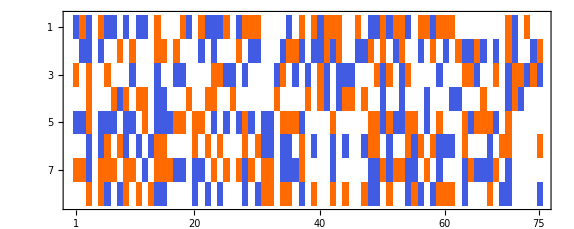

```mathematica
MatrixPlot[esthaplo[[3;;,2;;]]-old[[3;;,2;;]]]
```

```mathematica
(*****************************************************************************************************************************)
```